```mathematica
Needs["PlotLegends`"]
sqHeight = 90;
sqStd = 90;
minHeight = 60;
maxHeight = 200;
SQ[z_] = PDF[NormalDistribution[sqHeight, sqStd], z] / PDF[NormalDistribution[sqHeight, sqStd], sqHeight];
R[z_, r_] = (maxHeight - z) / (maxHeight - minHeight) * r;
J[z_] = SQ[z] - R[z];
Manipulate[Plot[SQ[z] - R[z, r],{z,minHeight,maxHeight}], {r, 0, 1}]
```

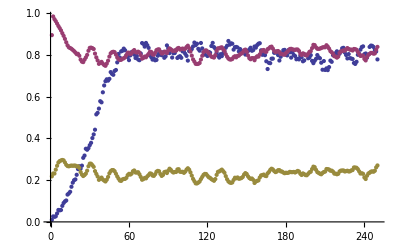

```mathematica
rdata = Import["~/Documents/Projects/rover/sandbox/all.txt", "Table"];
ListPlot[
Transpose[rdata][[{1,2,3}]] ]
```